From Try Kappa? vi I have an integral I can perform

```mathematica
integrand=(1+(1-b)hprime^2+b z0prime^2-b/(1-b)zprime^2);
```

```mathematica
gprime=√(zprime^2+(1-b)rhoprime^2);
hprimeSub=gprime/(1-b)-z0prime
```

-z0prime+(√((1-b) rhoprime^2+zprime^2))/(1-b)

```mathematica
integrandwSub=integrand/.{hprime->hprimeSub};
```

```mathematica
FullSimplify[integrandwSub]
```

1+rhoprime^2+z0prime^2+zprime^2-2 z0prime √(rhoprime^2-b rhoprime^2+zprime^2)

Try just the limiting case

For z’<z0’

```mathematica
Integrate[(1+hprime^2)^(-(κ+1)),{hprime,a,∞},Assumptions->{κ>3/2,a<0}]
```

(√π Gamma[1/2+κ])/(2 Gamma[1+κ])-a Hypergeometric2F1[1/2,1+κ,3/2,-a^2]

```mathematica
Integrate[(1+hprime^2)^(-(κ+1)),{hprime,0,∞},Assumptions->{κ>3/2}]
```

(√π Gamma[1/2+κ])/(2 Gamma[1+κ])

Negpart

```mathematica
Integrate[(1+hprime^2)^(-(κ+1)),{hprime,-a,∞},Assumptions->{κ>3/2,a>0}]
```

PosPart

```mathematica
Integrate[(1+hprime^2)^(-(κ+1)),{hprime,a,∞},Assumptions->{κ>3/2,a>0}]
```

(√π Gamma[1/2+κ])/(2 Gamma[1+κ])-a Hypergeometric2F1[1/2,1+κ,3/2,-a^2]

```mathematica
Integrate[(1+hprime^2)^(-(κ+1)),{hprime,a,∞},Assumptions->{κ>3/2,a>0}]
```

(√π Gamma[1/2+κ])/(2 Gamma[1+κ])-a Hypergeometric2F1[1/2,1+κ,3/2,-a^2]

```mathematica
Integrate[(1+hprime^2)^(-(κ+1)),{hprime,a,∞},Assumptions->{κ>3/2,Element[a,Reals],Element[hprime,Reals],Element[κ,Reals]}]
```

ConditionalExpression[-1/2 ⅈ (-1)^-κ Beta[-1/a^2,1/2+κ,-κ],a>0]

```mathematica
Integrate[(1+hprime^2)^(-(κ+1)),{hprime,a,∞},Assumptions->{κ>3/2,0<a<1}]
```

(√π Gamma[1/2+κ])/(2 Gamma[1+κ])-a Hypergeometric2F1[1/2,1+κ,3/2,-a^2]

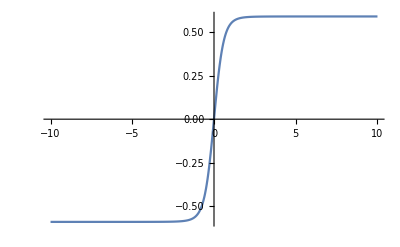

```mathematica
Plot[a Hypergeometric2F1[1/2,3,3/2,-a^2],{a,-10,10}]
```

```mathematica
thing=-1/2 ⅈ (-1)^-κ Beta[-1/a^2,1/2+κ,-κ]
```

-1/2 ⅈ (-1)^-κ Beta[-1/a^2,1/2+κ,-κ]

```mathematica
N[thing/.{κ->2,a->10}]
```

1.9578×10^-6-5.99404×10^-22 ⅈ

```mathematica
Plot3D[Im[Sqrt[x+I y]],{x,-4,4},{y,-4,4}]
```

-Graphics3D-

```mathematica
func[a_,κ_]:=(√π Gamma[1/2+κ])/(2 Gamma[1+κ])-a Hypergeometric2F1[1/2,1+κ,3/2,-a^2]
```

```mathematica
NIntegrate[func[a,
```

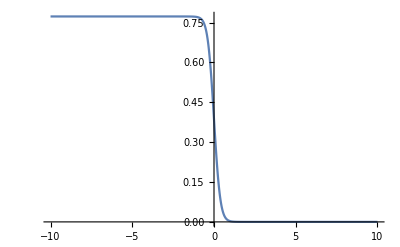

```mathematica
Plot[func[a,5],{a,-10,10}]
```

```mathematica
N[func[1000,1.5]]
```

2.50022×10^-13

### BRO

```mathematica
zNoughtPrime[deltaPhi_,T_,kappa_]:=√(deltaPhi/(T(kappa-3/2)))
```

```mathematica
funker[z0prime_,kappa_]:=NIntegrate[√π Gamma[kappa+1/2]/(2 Gamma[kappa+1])-zprimeS Hypergeometric2F1[1/2,1+kappa,3/2,-zprimeS^2],{zprimeS,-z0prime,∞},AccuracyGoal->20]
KFuncInverse[z0prime_,kappa_]:=(1/2 Gamma[kappa-1/2]/Gamma[kappa+1]+z0prime/(√π kappa)Hypergeometric2F1[1/2,kappa,3/2,-z0prime^2])^-1
barbKappaAsymp[z0prime_,kappa_]:=1+2 z0prime/(√π)KFuncInverse[z0prime,kappa] funker[z0prime,kappa]
```

```mathematica
zNoughtPrime[941,110,1.7]
```

6.54009

```mathematica
barbAsymp[deltaPhi_,T_]:=1+2(√(deltaPhi/T))/Erfc[-√(deltaPhi/T)] NIntegrate[Erfc[x],{x,-√(deltaPhi/T),∞}]
```

```mathematica
barbAsymp[941,110]
```

18.1094

```mathematica
barbKappaAsymp[zNoughtPrime[941,110,10000],10000]
```

18.1111

Plot below using absolute value for zPrimeS

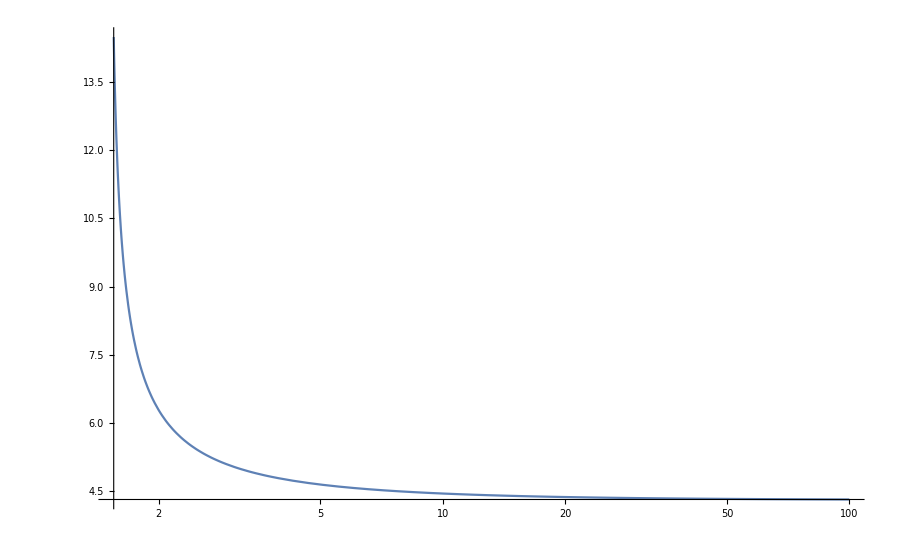

```mathematica
LogLinearPlot[barbKappaAsymp[zNoughtPrime[941,110,kappa],kappa],{kappa,1.55,100},PlotRange->{Full,Full},ImageSize->900]
```

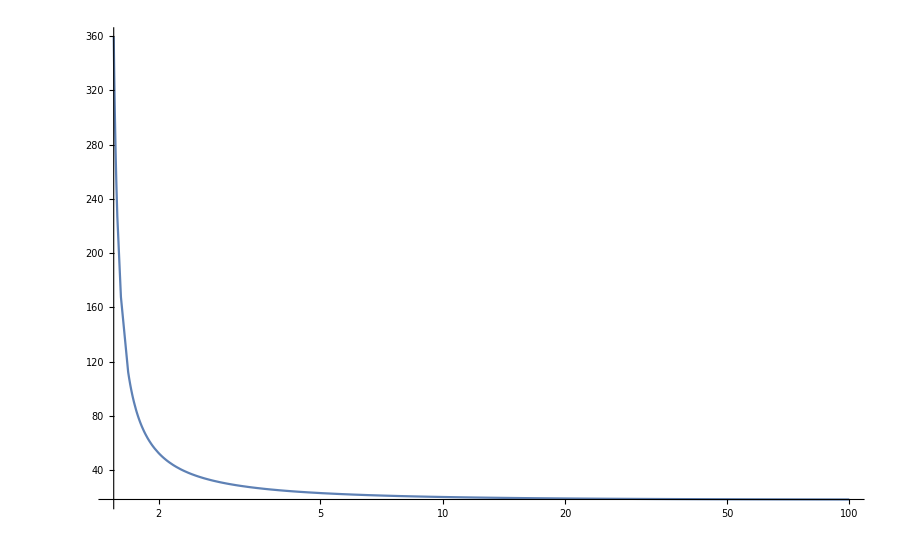

```mathematica
LogLinearPlot[barbKappaAsymp[zNoughtPrime[941,110,kappa],kappa],{kappa,1.55,100},PlotRange->{Full,Full},ImageSize->900]
```

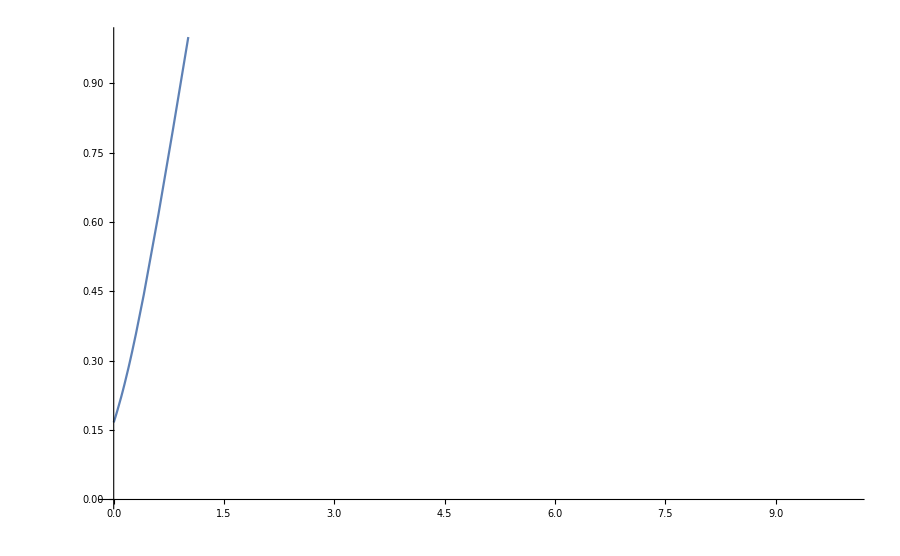

```mathematica
Plot[funker[z0prime,3],{z0prime,0,10},PlotRange->{Full,{0,1}},ImageSize->900]
```

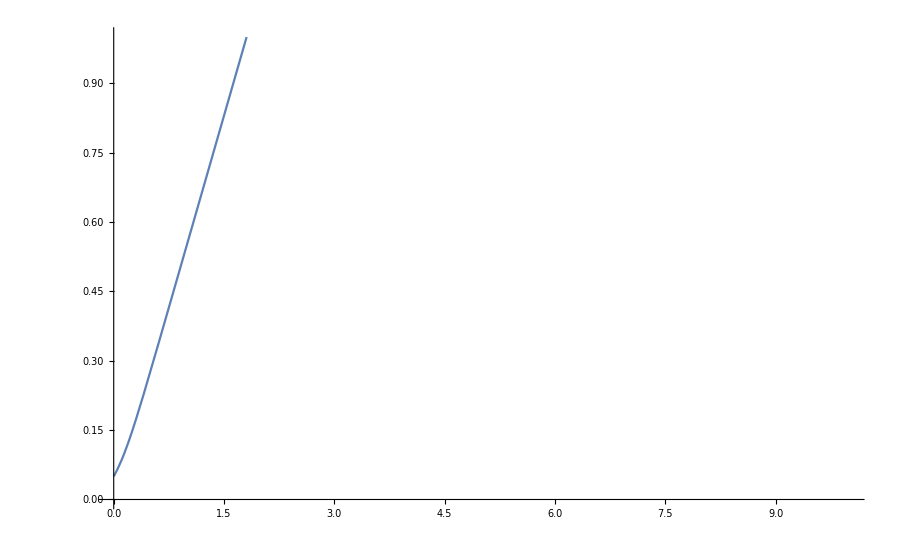

```mathematica
Plot[funker[z0prime,10],{z0prime,0,10},PlotRange->{Full,{0,1}},ImageSize->900]
```

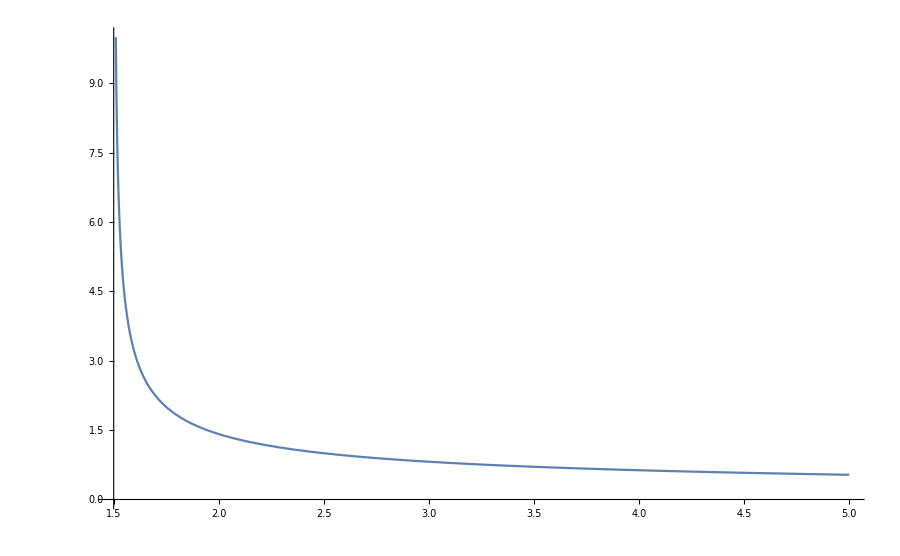

```mathematica
Plot[(kappa-3/2)^(-1/2),{kappa,1.5,5},PlotRange->{{1.5,5},{0,10}},ImageSize->900]
```

### Plot zNoughtPrime--is it huge?

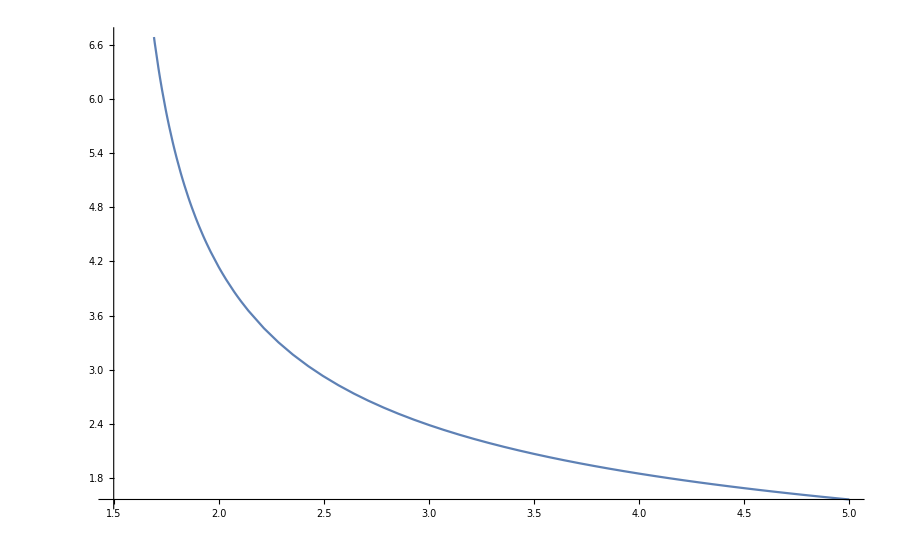

```mathematica
Plot[zNoughtPrime[941,110,kappa],{kappa,1.5,5},PlotRange->{{1.5,5},Automatic},ImageSize->900]
```

### No, it isn’t. (Though it does run to infinity for kappa->1.5.) Now KFuncInverse ...

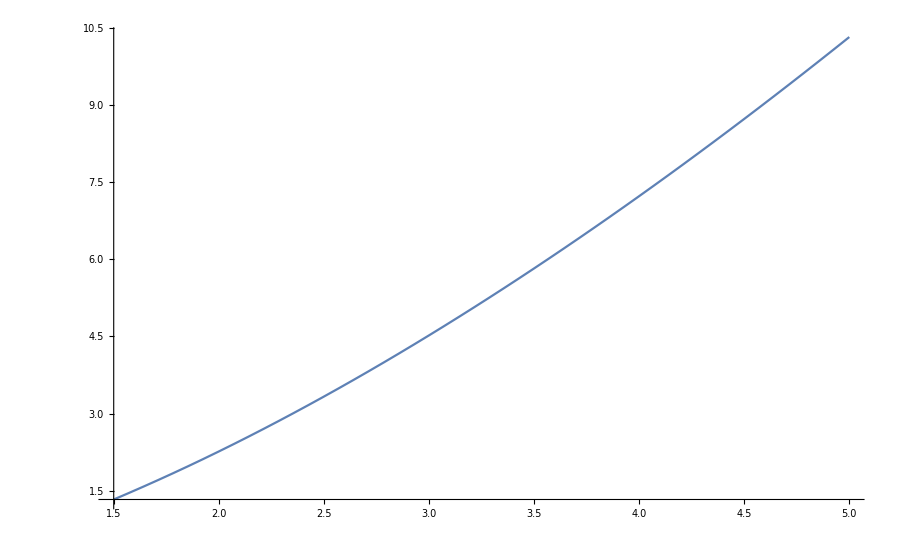

```mathematica
Plot[KFuncInverse[zNoughtPrime[941,110,kappa],kappa],{kappa,1.5,5},PlotRange->{{1.5,5},Automatic},ImageSize->900]
```

### Not unreasonable at all! Now---

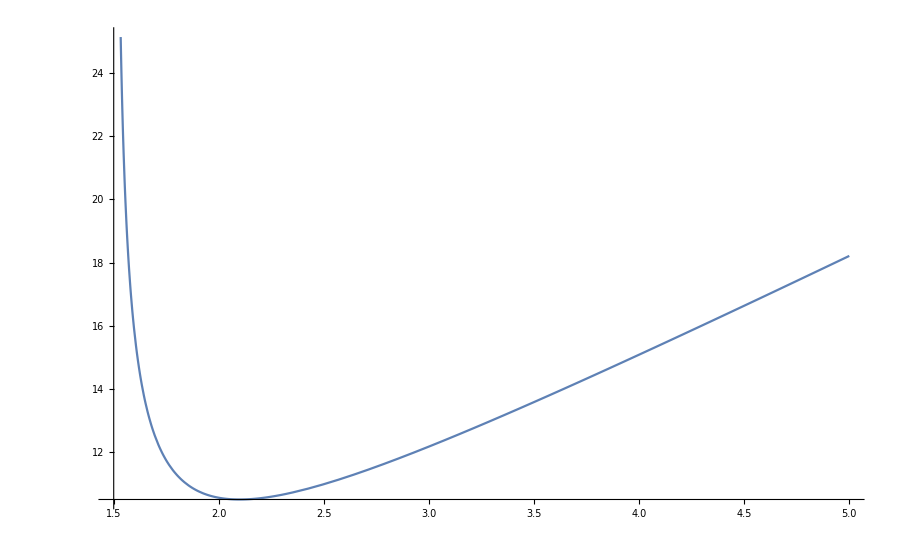

```mathematica
Plot[2 zNoughtPrime[941,110,kappa]/(√π)KFuncInverse[zNoughtPrime[941,110,kappa],kappa],{kappa,1.5,5},PlotRange->{{1.5,5},Automatic},ImageSize->900]
```

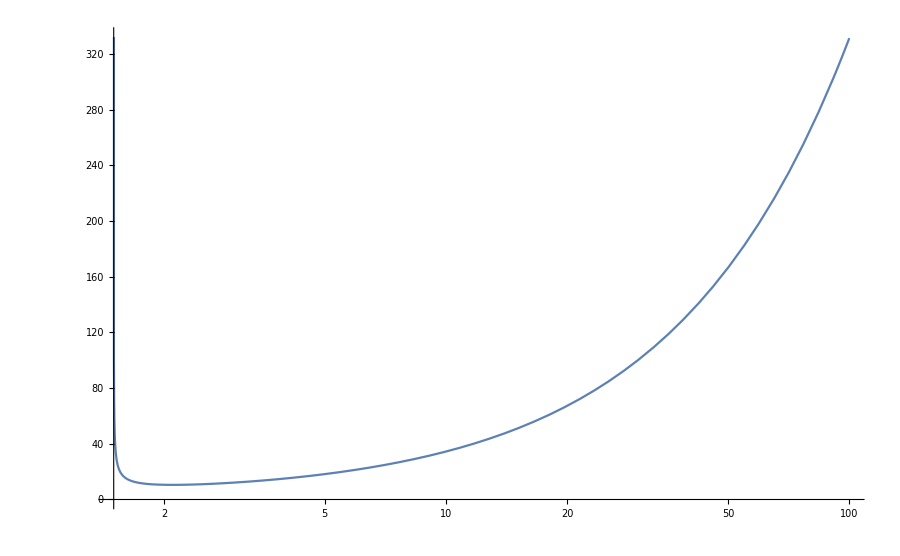

```mathematica
LogLinearPlot[2 zNoughtPrime[941,110,kappa]/(√π)KFuncInverse[zNoughtPrime[941,110,kappa],kappa],{kappa,1.5,100},PlotRange->{Full,Automatic},ImageSize->900]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in zprimeS near {zprimeS} = {8.16907×10^224}. NIntegrate obtained 3.94485843651878×10^27937 and 3.94485843651878×10^27937 for the integral and error estimates.

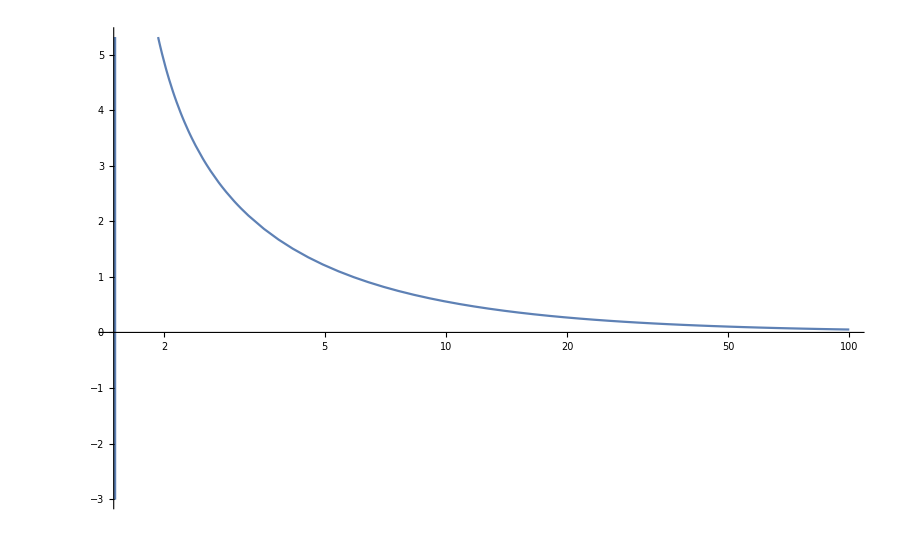

```mathematica
LogLinearPlot[funker[zNoughtPrime[941,110,kappa],kappa],{kappa,1.5,100},PlotRange->{Full,Automatic},ImageSize->900]
```